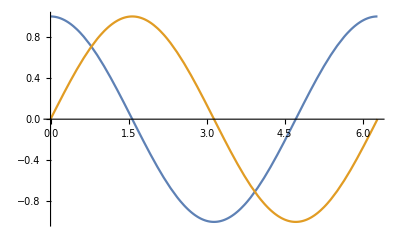

```mathematica
gr=Plot[{Cos[x],Sin[x]},{x,0,2 Pi}]
```

```mathematica
Export["plots.json",{
"labels"->{
"S34"->400,"phi3"->0.52,"phi4"->1.00,
"var1"->"x"
},
"data"->Cases[First@gr,Line[data_]:>data,-4]
},"Compact"->True]
```

plots.json